-(ⅇ^(-3 t/5) (√21 Cos[(√21 t)/5]+2 Sin[(√21 t)/5]))/(√21)

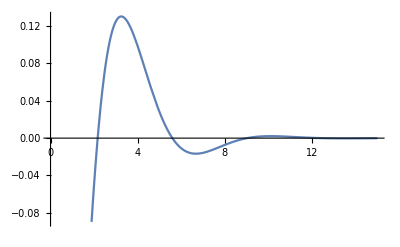

```mathematica
a=0;
Simplify[(-5(s+1))/(5(a*s+1)+(1+5s)(s+1))];
A = InverseLaplaceTransform[%,s,t];
Simplify[%]
Plot[A,{t,0,15}]
```

-(ⅇ^(-17 t/20) (√191 Cos[(√191 t)/20]+3 Sin[(√191 t)/20]))/(√191)

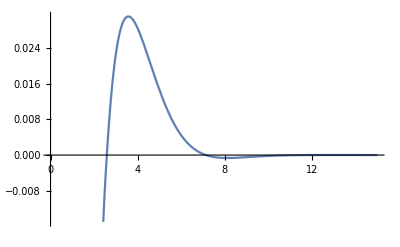

```mathematica
a=1/2;
Simplify[(-5(s+1))/(5(a*s+1)+(1+5s)(s+1))];
A = InverseLaplaceTransform[%,s,t];
Simplify[%]
Plot[A,{t,0,15}]
```

1/68 ⅇ^(-1/5 (8+√34) t) (-34-3 √34+(-34+3 √34) ⅇ^((2 √34 t)/5))

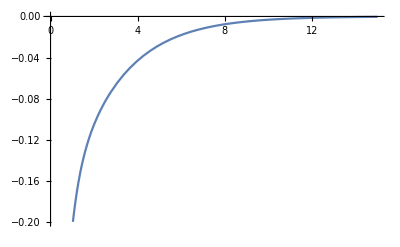

```mathematica
a=2;
Simplify[(-5(s+1))/(5(a*s+1)+(1+5s)(s+1))];
A = InverseLaplaceTransform[%,s,t];
Simplify[%]
Plot[A,{t,0,15}]
```

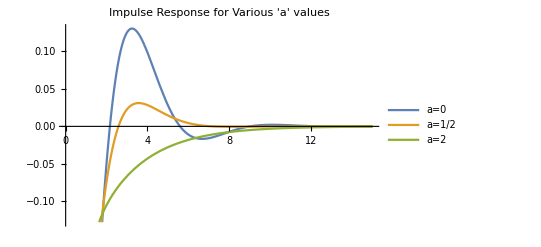

```mathematica
Plot[{-(ⅇ^(-3 t/5) (√21 Cos[(√21 t)/5]+2 Sin[(√21 t)/5]))/(√21), -(ⅇ^(-17 t/20) (√191 Cos[(√191 t)/20]+3 Sin[(√191 t)/20]))/(√191),1/68 ⅇ^(-1/5 (8+√34) t) (-34-3 √34+(-34+3 √34) ⅇ^((2 √34 t)/5))},{t,0,15},PlotLegends->{"a=0","a=1/2","a=2"},PlotLabel-> "Impulse Response for Various 'a' values"]
```